# Anonymous functions

Math 250 - Mathematical Computing
Christopher Hanusa

## 6.1 Overview

In this tutorial, we learn how Mathematica defines anonymous functions and how to develop more complex functions for one or more inputs.

## 6.2 The structure of functions in Mathematica

Let’s learn a more advanced way to define functions

Before we do that, let’s look at the internal format in which Mathematica defines a function.

### Using Function

Instead of defining our “square” and “addEmUp” functions like in the previous tutorial, we could have instead written:

```mathematica
squareMe[x_]:=x^2
```

```mathematica
alternateSquare=Function[x,x^2]
```

Function[x,x^2]

```mathematica
addEmUp[x_,y_]:=x+y
```

```mathematica
alternateAddEmUp=Function[{x,y},x+y]
```

Function[{x,y},x+y]

Then we can apply these functions in the same way.

```mathematica
alternateSquare[20]
```

400

```mathematica
alternateAddEmUp[-Pi,3Pi]
```

2 π

Here, we are using the Function command, which has two inputs.  The first input to Function is the input variable to the function (or list of input variables), and the second input to Function is the coder-defined output of the function.

NOTE: We used set (=) instead of set delayed (:=), and there was no need to use underscores.  All these things are taken into account by the Function command.

We can also apply a function written using a Function command without giving it a name.

```mathematica
Function[x,x^2][20]
```

400

```mathematica
Function[{x,y},x+y][2000,6994]
```

8994

This code is cumbersome, but it leads us to a widely used technique, that of anonymous functions.

## 6.3 Defining an anonymous function

### Anonymous functions

Suppose you want to code in a function that you only want to apply once and you don’t want to worry about giving it a name.  Then you can create an  anonymous function.  They are a bit confusing at first, but become very handy as you become proficient.

(RHS[#])&   or   (RHS[#1,#2])&

(Again, RHS stands for Right Hand Side, and represents the actual function you want to apply to the variables.)

The # symbol is called a Slot and represents an anonymous input variable.  While in the Function command you would define your right hand side around the input variable x, here wherever you would put x, you replace it by a # symbol. If your function has  more than one input, use #1, #2, #3, ... to represent the first, second, third, ... inputs in order.

The & symbol represents the end of the function and that signals to Mathematica that what follows should be the inputs to the function.

To increase readability, you can use parentheses ( ) to delimit the beginning and end of your anonymous function.

### Examples

The anonymous versions of the above functions are

```mathematica
(#^2)&
```

and

```mathematica
(#1+#2)&
```

Here are some examples of them in action:

```mathematica
(#^2)&[Pi]
```

π^2

```mathematica
(#1+#2)&[3,4]
```

7

Notice that when calling anonymous functions, you still need to use square brackets around the inputs.

## 6.4 Anonymous functions and Map

An especially handy place to use anonymous functions is in tandem with the Map command. You might have a list of objects and want to apply a function to the whole list, but don’t especially want to define the function outright.  You can use the Map command and an anonymous function to do it!

Here is an example that squares all the entries in a list.

```mathematica
mylist=Range[4,17,3]
```

{4,7,10,13,16}

```mathematica
Map[#^2&,mylist]
```

{16,49,100,169,256}

Example 6.4.1.  Create a list that contains the regular polygons that has the number of sides given by mylist.

```mathematica
Graphics[RegularPolygon[7]]
```

-Graphics-

```mathematica
Map[Graphics[RegularPolygon[#]]&,mylist]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Example 6.4.2.  Graph the following functions from -5 to 5.

```mathematica
functions={Sin[x],x^2,ArcTan[x],Log[x]};
```

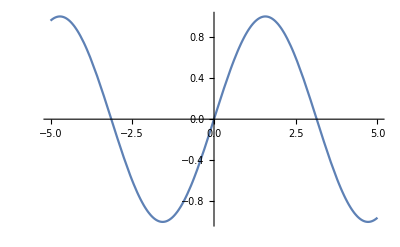

```mathematica
Plot[Sin[x],{x,-5,5}]
```

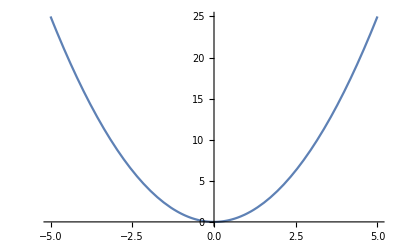
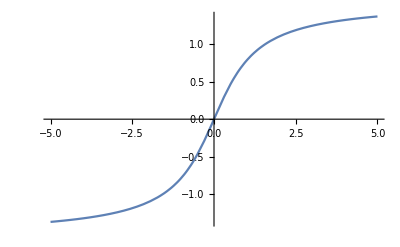
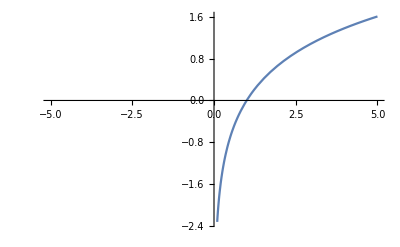
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[Plot[#,{x,-5,5}]&,functions]
```

## 6.5 Anonymous functions and MapThread

When you want to combine information from multiple lists entry by entry through an anonymous function, you need to use the MapThread command instead.

Suppose you have lists of the x-coordinates, y-coordinates, and z-coordinates of some datapoints and you want to combine them into a list of three-dimensional coordinates.

```mathematica
xlist={1,1,2,3,5,8,13};
ylist ={2,4,8,16,32,64,128};
zlist ={0,-1,-2,-3,-4,-5,-6};
```

The corresponding anonymous function is {#1,#2,#3}& and the code that does this is

```mathematica
{#1,#2,#3}&[X1,Y1,Z1]
```

{X1,Y1,Z1}

```mathematica
MapThread[{#1,#2,#3}&,{xlist,ylist,zlist}]
```

{{1,2,0},{1,4,-1},{2,8,-2},{3,16,-3},{5,32,-4},{8,64,-5},{13,128,-6}}

Remember that your lists of data need to be the same length!

Example 6.5.1.  Recreate the following list of colorful days of the week using MapThread instead.

{Monday,Tuesday,Wednesday,Thursday,Friday}

```mathematica
daysOfWeek={"Monday","Tuesday","Wednesday","Thursday","Friday"};
colors={Red,Orange,Yellow,Green,Blue};
```

```mathematica
Style["Monday",Red]
```

Monday

```mathematica
MapThread[Style[#1,#2]&,{daysOfWeek,colors}]
```

{Monday,Tuesday,Wednesday,Thursday,Friday}

Example 6.5.2.  Give the days of the week different fonts and font sizes.

```mathematica
Style["Monday",Red,FontFamily->"Algerian",FontSize->14]
```

Monday

```mathematica
fonts={"Times","Arial","Helvetica","Alegreya SC","Algerian"};
sizes={50,30,20,5,15};
```

```mathematica
MapThread[Style[#1,#2,FontFamily->#3,#4]&,{daysOfWeek,colors,fonts,sizes}]
```

{Monday,Tuesday,Wednesday,Thursday,Friday}

```mathematica
Style["Monday",Red,FontFamily->"Times",FontSize->50]
```

Monday

```mathematica
MapThread[Style[#1,#2,#3,#4]&,{daysOfWeek,colors,fonts,sizes}]
```

{Monday,Tuesday,Wednesday,Thursday,Friday}

```mathematica
Style["Monday",Red,"Times",100]
```

Monday